# C & Q Chaos III - Action-angle coordinates

In this notebook we will delve deeper into integrability, how it is defined and what is it exactly that makes us say that a system is non-integrable. We will then go and discuss the homoclinic tangle that is one of the few analytical proofs of chaoticity.

## Take a step back: Integrable systems

- Every 1 DOF autonomous system is integrable - the shape of its phase - space trajectories are simply given by constant energy surfaces .
 - If we just add N 1DOF Hamiltonians that depend on independent DOFs, the result will again be integrable . E . g . for N=2 DOFs :

```mathematica
Hsep[px_,x_,py_,y_] := Hx[px,x] + Hy[py,y];
```

- Then the pairs of coordinates fulfill equations that are not coupled and the Hamiltonians Hx, Hy are conserved separately.

```mathematica
px'==-D[Hsep[px,x,py,y],x]
x'==D[Hsep[px,x,py,y],px]
py'==-D[Hsep[px,x,py,y],y]
y'==D[Hsep[px,x,py,y],py]
```

- For bound motions, the motions are oscillations in N different DOFs. Since each oscillation is a topological circle, the composite motion is a product of N circles. That is known as an N-torus.
- Is every integrable Hamiltonian like this? In a way yes, but seeing it from the actual expression of the Hamiltonian can be hard.

## Simple example: Motion in a central potential

Consider motion in a plane in a radial potential.

```mathematica
Hc[px_,x_,py_,y_] := 1/2(px^2+py^2) + Pot[√(x^2+y^2)];
```

Is this Hamiltonian separable at face value? No, but it is integrable as we will see .

#### Transform the Hamiltonian to polar coordinates

(Recall that momenta are forms, not vectors, they transform with an inverse Jacobian.)

#### Solution

```mathematica
xpol  = r Cos[ϕ];
ypol = r Sin[ϕ];
(*Find the Jacobian and inverse Jacobian of the transform:*)
J ={ {D[xpol,r],D[xpol,ϕ]},{D[ypol,r],D[ypol,ϕ]}}
iJ = Inverse[J]
{pxpol,pypol} = {pr,pϕ}.iJ//Simplify
 Hc[pxpol,xpol,pypol,ypol]//Simplify[#,{r>0}]&
```

```mathematica
Hpol[pr_,r_,pϕ_,ϕ_]:=1/2 (pr^2+pϕ^2/r^2+2 Pot[r]);
```

ϕ is a cyclical coordinate (the Hamiltonian is independent of it), so L =pϕ is conserved

#### The r,pr trajectory shape is determined by the condition that E=Hpol and L=pϕ are constant. Also, the ϕ,pϕ shape is trivially determined by this constraint. Plot some of the shapes using the potential below.

```mathematica
Pot[r_] := -1/r - 1/r^3;
```

#### Solution

```mathematica
ContourPlot[Hpol[pr,r,4,0],{r,1,50},{pr,-0.5,0.5},Contours->{-0.03,-0.025,-0.01,0,0.01,0.025},FrameLabel->{r,pr}]
DensityPlot[Hpol[pr,r,4,0],{r,1,50},{pr,-0.5,0.5}]
ContourPlot[pϕ,{ϕ,0,2π},{pϕ,0,5},FrameLabel->{ϕ,pϕ}]
```

```mathematica
Plot also the shape this defines in the ϕ,r,pr plane for a selected bound motion.Plot also the shape this defines in the ϕ,r,pr plane for a selected bound motion.
```

#### Plot the hypersurface defined by the E=const. L=const. condition in the r,pr,ϕ space for a suitable bound motion.

Hint: Try an embedding into Euclidean x,y,z where we remap r=√(x^2+y^2), ϕ=ArcTan[y,z], and pr=z.

#### Solution

```mathematica
ContourPlot3D[Hpol[z,Sqrt[x^2+y^2],4,ArcTan[y,x]]==-0.025,{x,-32,32},{y,-32,32},{z,-0.3,0.3}]
```

#### Now find also the corresponding r,pr,ϕ trajectory and plot it on top of the torus using ParametricPlot3D[] and Show[]

#### Solution

```mathematica
Traj = {pr->pr[t],r->r[t],ϕ->ϕ[t]};
EOM = {pr'[t]==(-D[Hpol[pr,r,pϕ,ϕ],r]/.Traj),r'[t]==(D[Hpol[pr,r,pϕ,ϕ],pr]/.Traj),ϕ'[t]==(D[Hpol[pr,r,pϕ,ϕ],pϕ]/.Traj)}
ri = 15; 
pϕi = 4;
E0 = -0.025;
initSol = Solve[Hpol[pr,ri,pϕi,ϕ]==E0,pr];
Init = {r[0]==ri,ϕ[0]==0,pr[0]==(pr/.initSol[[2]])}
TrSol =Block[{pϕ=pϕi},NDSolve[Join[EOM,Init],{r[t],pr[t],ϕ[t]},{t,0,100000}]]
```

```mathematica
ParametricPlot3D[{r[t]Cos[ϕ[t]],r[t]Sin[ϕ[t]],pr[t]}/.TrSol,{t,0,20000}]
Show[ContourPlot3D[Hpol[z,Sqrt[x^2+y^2],4,ArcTan[y,x]]==-0.025,{x,-32,32},{y,-32,32},{z,-0.3,0.3}],ParametricPlot3D[{r[t]Cos[ϕ[t]],r[t]Sin[ϕ[t]],pr[t]}/.TrSol,{t,0,20000}]]
```

#### Build and plot a different “snapshot set”, by recording r, pr when ϕ mod 2π == 0

#### Solution

```mathematica
RPrSnaps = Block[{pϕ = pϕi},Reap[ NDSolve[Join[EOM, Init,{WhenEvent[Mod[ϕ[t],2π]==0,Sow[{r[t],pr[t]}]]}], {r[t], pr[t], ϕ[t]}, {t, 0, 100000}]]]
```

```mathematica
ListPlot[RPrSnaps[[2,1]]]
```

This is closely analogous to the snapshots we did for the driven mathematical pendulum. However, here we see this amounts to a cross-section of the flow. In some sense, we did a slice through the torus plotted above. 

In principle, we could have chosen any other condition Ψ(r,pr,ϕ,pϕ)==0 which, when crossed, is used to record the state. This would simply lead to a slice of the structures by a different hypersurface. This type of condition is known as a Poincaré surface of section. It is really useful to dissect the dynamics of systems with 2DOFs (or “effectively 2DOFs”).

## Liouville integrability

An autonomous Hamiltonian system of N degrees of freedom is Liouville integrable if there exist N functionally independent constants of motion
F_1,F_2,... F_N​ where:
 - The gradients of the functions F_i are linearly independent almost everywhere.
 - The Poisson bracket of any pair of the constants of motion vanishes.
(Often one chooses F_1=H.)

Given the above is satisfied the Liouville-Arnold theorem states that:
 - The hypersurfaces defined by constant F_1,F_2,... F_N are topologically products of the real line and circles, corresponding to bounded motion and possibly unbounded motion. (For purely bounded motion we get a simple N-dimensional torus.)
 - The motion can be solved for by quadratures: one-dimensional integral expressions that often implicitly define the solution.
 - There exist pairs of local canonical coordinates J_i,ψ^i, i=1...N such that J_i represent an alternative set of constants of motion, the Hamiltonian is transformed into H(J_i) (no dependence on ψ^i), and ψ^i'= dH/dJ_i = Ω^i(J_j)=const. These are known as Action-Angle coordinates (I will abbreviate them with AA).

Some notes:
-  Finding the transformation to the full set of AA coordinates is often harder than finding the exact solution of the equations of motion themselves. However, finding just the angles is exactly as hard as just solving the equations of motion by quadrature.
- Angles are great for perturbation theory, and you do not use the actions for that!
- Actions are great because they represent gauge/coordinate invariants.
- The Ω^i are known as the fundamental frequencies of motion. They can be extracted numerically (or even experimentally) from the motion just by looking at harmonics of various time-series from the system. They are also gauge/coordinate invariant.

## Constructing AA coordinates - Hamilton-Jacobi equation

Recall from your analytical-mechanics course that coordinate transforms could be obtained from generating functions. The transformation to AA coordinates is obtained from a generating function of the second kind that fulfills the Hamilton-Jacobi equation. For example, for a 1DOF system

```mathematica
D[S[x,t],t] == Ham[px,x]/.{px-> D[S[x,t],x]}
```

S^(0,1)[x,t]==Ham[S^(1,0)[x,t],x]

This is typically a non-linear PDE that may be quite hard to solve. 

The set of conserved quantities above guarantees that one can choose a set of N separation constants α_1,...,α_N corresponding to the values F_1,...,F_N. Once solving for S, one could In principle, one could use the α_1,...,α_N as canonical momenta, but the conjugate variables would not be 2π-periodic. In order to get 2π-periodic angles, one has to instead reexpress the α_i in terms of actions. For example, for 1DOF the action is expressed as

```mathematica
Jx[α]==1/π Integrate[D[Ssol[x,t0,α],x],{x,xturn1,xturn2}];
```

- The general expression would involve integrating a similar expression over a loop winding around the torus. 
- The winding of the loop over the torus must be single-winding (no repeating loops). There are N such loops around an N-dimensional torus, which yields N  independent actions. 
- The definition of the action depends only on the homotopy class of the loop (the “topology” of the loop).
- There is not a unique set of actions, but given one set, another one is obtained only by changing the homotopy classes. It turns out that any other set is then given by integer lattice transforms with determinant 1.

After all this work, one has J_x(α), which has to be inverted to obtain α(J_x) and substituted into S_final(x,t;J_x) =S_sol(x,t;α(J_x)). Finally, one obtains the angle

```mathematica
ψx[x,t,Jx] == D[Sfinal[x,t,Jx],Jx]
```

Generally, one obtains N angles from derivatives wrt N actions. For autonomous Hamiltonian systems the ψ coordinates are independent of time.

One of the hard steps is now inverting the relation ψ^x(x;J_x) to x(ψ^x;J_x). Once you have that, you can transform the Hamiltonian to the new coordinates and you will obtain the Hamiltonian in normal form H_norm= H_norm(J). 
The theory also tells us that the angles evolve homogeneously in time

```mathematica
ψ[x[t],Jx] == D[Subscript[H, norm][Jx],Jx] (t-t0)
```

In particular, the knowledge of the function x(ψ^x;J_x) then essentially expresses the general solution of the equations of motion.

There are a couple hard steps in the procedure above. There are work-arounds when we are unable to carry out some of the inversions etc and this formalism is still useful when you cannot fully transform to AA coordinates.

## AA for mathematical pendulum

#### Hamilton-Jacobi equation

```mathematica
Hmp[px,x] = 1/2 px^2 - Cos[x];
HJEq =D[S[x,t],t] == Hmp[px,x]/.{px-> D[S[x,t],x]}
```

S^(0,1)[x,t]==-Cos[x]+1/2 (S^(1,0)[x,t])^2

```mathematica
(*Additive separation Ansatz*)
```

```mathematica
HJAnsatz = HJEq/.{S->Function[{x,t},En t +Sx[x]]}
```

En==-Cos[x]+1/2 Sx'[x]^2

```mathematica
(*Mathematica can integrate this for you since it is a reasonably simple ODE*)
```

```mathematica
SxSols = DSolve[HJAnsatz,{Sx[x]},{x}]//FullSimplify[#,{En+Cos[x]>0}]&
(*Note that the assumption will not be true in the "rotation" part of phase space En>1, only for librations En<1.*)
```

{{Sx[x]→C[1]-(2 EllipticE[x/2,2/(1+En)])/(√(1/(2+2 En)))},{Sx[x]→C[1]+(2 EllipticE[x/2,2/(1+En)])/(√(1/(2+2 En)))}}

```mathematica
(*Check solution*)
```

```mathematica
D[Sx[x]/.SxSols,x]//FullSimplify[#,{-1<En<1}]&
```

{-√2 √(En+Cos[x]),√2 √(En+Cos[x])}

#### Find the action coordinate

```mathematica
(*Find turning points*)
xtpSols = Solve[En+Cos[x]==0,x,Assumptions->{-π<x<π,-1<En<1}]
```

{{x→-ArcCos[-En]},{x→ArcCos[-En]}}

```mathematica
(*Find Action*)
```

4 √2 √(1+En) EllipticE[1/4 (π+2 ArcSin[En]),2/(1+En)]

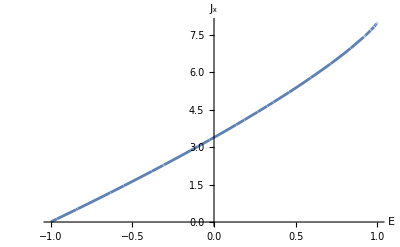

```mathematica
JxE = Integrate[√(2(En+Cos[x])),{x,(x/.xtpSols[[1]]),(x/.xtpSols[[2]])},Assumptions->{-1<En<1}]
Plot[JxE,{En,-1,1},AxesLabel->{"E",Subscript[J, x]}]
```

```mathematica
(*Invert relation to obtain E(J)*)
Solve[JxE==Jx,En]
(*There is no standard inverse for the EllipticE[] function...*)
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[4 √2 √(1+En) EllipticE[1/4 (π+2 ArcSin[En]),2/(1+En)]==Jx,En]

#### Find the angle, invert

```mathematica
(*No matter, let us assume we know E(J) and use the implicit function theorem*)
```

```mathematica
ψSol = D[(Sx[x]/.SxSols[[1]]),En]/D[JxE,En]//FullSimplify[#,{-1<En<1}]&
Manipulate[Plot[ψSol/.{En->Ener},{x,-π,π}]//Quiet,{Ener,-1,1}]
```

-EllipticF[x/2,2/(1+En)]/(2 EllipticF[1/4 (π+2 ArcSin[En]),2/(1+En)])

```mathematica
xψSol = Solve[ψSol==ψ,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-2 JacobiAmplitude[2 ψ EllipticF[1/4 (π+2 ArcSin[En]),2/(1+En)],2/(1+En)]}}

#### Profit

```mathematica
(*The Hamiltonian in normal form is En(J) and does not have a standard closed-form expression. However, its derivatives (the frequencies) can be expressed:*)
```

```mathematica
Ωx = 1/D[JxE,En]//FullSimplify
xtSol = x/.xψSol[[1]]/.{ψ->Ωx t}//FullSimplify
pxtSol = √(2(En + Cos[x]))/.{x->xtSol}//FullSimplify
pxtSol = D[x/.{x->xtSol},t]
```

(√(1+En))/(2 √2 EllipticF[1/4 (π+2 ArcSin[En]),2/(1+En)])

-2 JacobiAmplitude[(√(1+En) t)/(√2),2/(1+En)]

√2 √(En+Cos[2 JacobiAmplitude[(√(1+En) t)/(√2),2/(1+En)]])

-√2 √(1+En) JacobiDN[(√(1+En) t)/(√2),2/(1+En)]

```mathematica
Manipulate[Plot[Mod[xtSol-π,2π]-π/.{En->Ener},{t,0,10π},AxesLabel->{t,x}]//Quiet,{Ener,-1,1}]
Manipulate[Plot[pxtSol/.{En->Ener},{t,0,10π},AxesLabel->{t,px}]//Quiet,{Ener,-1,1}]
Manipulate[ParametricPlot[{Mod[xtSol-π,2π]-π,pxtSol}/.{En->Ener},{t,0,10π},PlotRange->{{-π,π},{-2,2}}]//Quiet,{Ener,-1,1}]
```

#### Exercise 1: Create an animation of the motion using Animate[]

#### Exercise 2: Try to reproduce this using another potential, say, the “Mexican hat” -x^2+x^4

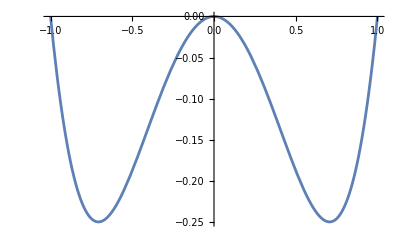

```mathematica
Plot[-x^2+x^4,{x,-1,1}]
```

## Some more remarks

- When a Hamiltonian does not depend on a canonical coordinate, the conjugate momentum is always proportionate to an actions.
 - This was the case of the angular momentum L in the motion of the central potential, which is just an action. Interestingly, the ϕ is not an AA-type angle though! 
 - Another example of a momentum proportional to an action that we encountered was the momentum p_τ we encountered in the time-dependent Hamiltonian. In that case, the 2π-periodic τ was an angle variable.
 - Interestingly enough, the Hamiltonian of a harmonic oscillator in normal form is also just H(J_x) = ω J_x where ω is constant oscillation frequency.

## Perturb the pendulum

Now we are better equipped to understand what the perturbations to the pendulum. For the system to be integrable, the snapshots should look like cutting through a torus T^2, which would be a circle (unless you are unlucky and cut tangentially). So we know we are looking at non-(Liouville)-integrability, since the motion is bound, but not restricted to tori. 

What else can we say about it? Let us examine the Hamiltonian:

```mathematica
Hna[p_,x_,pτ_,τ_] :=  1/2 p^2 - Cos[x] +ϵ Cos[x] Sin[τ] + pτ;
```

Now let us transform to the AA coordinates of the unperturbed system (at ϵ=0). We get:

```mathematica
HAA[Jx,ψx,pτ,τ]==H0[J] +pτ +ϵ Cos[x/.xψSol[[1]]]Sin[τ]
```

HAA[Jx,ψx,pτ,τ]==pτ+H0[J]+ϵ Cos[2 JacobiAmplitude[2 ψ EllipticF[1/4 (π+2 ArcSin[En]),2/(1+En)],2/(1+En)]] Sin[τ]

The basic question is where (and with which degree of convergence) can we still represent the Hamiltonian in normal form, which means eliminating the dependence on the angle variables ψ,τ. We could try simply guessing a good approximate Hamiltonian by averaging out the angle dependence. 

In our case this yields the original Hamiltonian and we know it fails badly near the saddle point (unstable equilibrium). Why?

The answer is in the so-called homoclinic tangle.
-Graphics--Graphics-
 - In the time-dependent system, we can understand the Poincaré surfaces of section as a discrete map. These maps have fixed points γ (points that are mapped onto themselves after an iteration) that are at the fixed points of the isolated system when ϵ=0.
 - They also have stable and unstable manifolds W^s(γ), W^u(γ), which may be homoclinic. Under perturbation, the homoclinic manifold often bifurcates into unstable and stable manifolds again. 
 - However, since the perturbed W^s(γ), W^u(γ) are close, they can transversally intersect. The intersection lays both on W^s(γ), W^u(γ), which is an invariant property under iteration. 
 - This means if one transversal intersection is present, infinitely more have to be as well. As a result a “tangle” of infinitely folding intersections appear.
 - It was shown by Smale in the 1960s that this leads to “horseshoe” dynamics that can be proven to imply what is known as chaos, an exponential divergence of any nearby trajectories in the set. This is known as the Smale-Birkhoff homoclinic theorem.
 - What we are seeing in the perturbed mathematical pendulum is the consequence of the homoclinic tangle at the saddle point.

### The Melnikov method

The distance between the manifolds W^s(γ), W^u(γ) can in fact be computed by perturbation theory, the method is known as Melnikov’s method. The formula for a time-dependent perturbation is (see Wiggins - Introduction to Applied Nonlinear Dynamical Systems and Chaos)
-Graphics-

Where H_0 is the zeroth order Hamiltonian, H_1 is the perturbation, and the phase-space trajectory is along the unperturbed homoclinic orbit. When this function expressed as a function of t0 oscillates through zero, it proof of chaos.

### Exercise: (Semester project) try to compute the Melnikov integral for some system.

## The Standard map

The Standard map is the map (discrete dynamical system) that one obtains from the “kicked rotor”. The rotor moves freely but once per a time interval it is “kicked from above”. This means that it gains an impulse that depens on the height where it is at.

```mathematica
Hkr[px,x,t] == 1/2 px^2 - K Cos[x]Sum[δ[t-n],{n,1,∞}]
```

This system is non - smooth, but it defines a Poincaré map in closed form while exhibit chaos so it is often used as a model. Interestingly, since this is like a “mathematical pendulum broken into discrete impulses”, it has a somewhat similar phase space portrait. The period of the forcing is 1 in the units here.

```mathematica
x[n+1] == Mod[x[n]+p[n],2π]
px[n +1] == px[n] + K Sin[x[n+1]]
```

x[1+n]==Mod[p[n]+x[n],2 π]

px[1+n]==px[n]+0.97 Sin[x[1+n]]

```mathematica
(*Define the Standard Map as a compiled function for speed*)
standardMap=Compile[{{px,_Real},{x,_Real},{k,_Real}},
Module[{xNew,pxNew},
xNew=Mod[x+px,2 Pi];
pxNew=px+k*Sin[xNew];
{pxNew,xNew}
],
CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True
];
```

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

```mathematica
Manipulate[ListPlot[NestList[standardMap[#1,#2,k]&,{1,π/2},10000]],{k,0,10}]
```

Function::slotn: Slot number 2 in standardMap[#1,#2,FE`k$$405]& cannot be filled from (standardMap[#1,#2,FE`k$$405]&)[{1,π/2}].

CompiledFunction::cfsa: Argument {1,π/2} at position 1 should be a machine-size real number.

Function::slotn: Slot number 2 in standardMap[#1,#2,FE`k$$405]& cannot be filled from (standardMap[#1,#2,FE`k$$405]&)[{{1,Mod[1+#2,2 π]},{π/2,Mod[π/2+#2,2 π]}}].

CompiledFunction::cfsa: Argument {{1,Mod[1+#2,2 π]},{π/2,Mod[π/2+#2,2 π]}} at position 1 should be a machine-size real number.

Function::slotn: Slot number 2 in standardMap[#1,#2,FE`k$$405]& cannot be filled from (standardMap[#1,#2,FE`k$$405]&)[{{{1,Mod[1+#2,2 π]},{Mod[1+#2,2 π],Mod[Mod[Plus[«2»],Times[«2»]]+#2,2 π]}},{{π/2,Mod[π/2+#2,2 π]},{Mod[π/2+#2,2 π],Mod[Mod[Plus[«2»],Times[«2»]]+#2,2 π]}}}].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

CompiledFunction::cfsa: Argument {{{1,Mod[1+#2,2 π]},{Mod[1+#2,2 π],Mod[Mod[1+Slot[«1»],2 π]+#2,2 π]}},{{π/2,Mod[π/2+#2,2 π]},{Mod[π/2+#2,2 π],Mod[Mod[Times[«2»]+Slot[«1»],2 π]+#2,2 π]}}} at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

### Exercise: Find the homoclinic tangle in the standard map

-Graphics-
How to:
- Take the fixed points of the map x=0,π
- Compute the Jacobian of the map, find its eigenvectors
- Take a number of points (say 100) placed along very small distance (say within 10^-7 in code units) along one of the eigendirections. 
- Iterate the points many times (say 1000).
- Repeat with both eigendirections
- Plot the result.
(You can take inspiration from https://galileo-unbound.blog/2020/08/24/henri-poincare-and-his-homoclinic-tangle/)